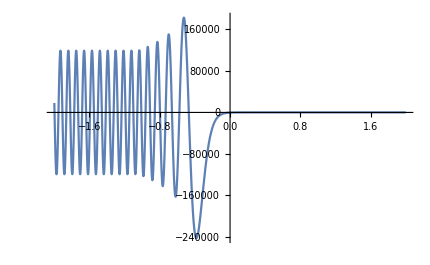

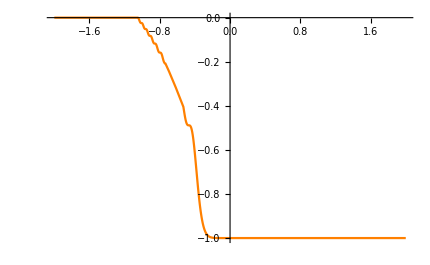

```mathematica
a=1;
b=-0.1+ⅈ*0.0001;
k=70;
t=0;
A=1;
X0=2;

Epsilon = Function[x,Piecewise[{{1,Re[a*x^2+b]>1}},a*x^2+b]];
P[x_]={{Epsilon[x],0,0},{0,Epsilon[x],0},{0,0,Epsilon[x]}};

(*TE-wave*)
TESystem = 
{Ereal'[x]==-k*Bimg[x],
Eimg'[x]==k*Breal[x],
Breal'[x]==-k*(Im[Epsilon[x]]*Ereal[x]+(Re[Epsilon[x]]-Sin[t]^2)*Eimg[x]),
Bimg'[x]==k*(Ereal[x]*(Re[Epsilon[x]]-Sin[t]^2)-Im[Epsilon[x]]*Eimg[x]), 
Ereal[X0]==A,Breal[X0]==A*Cos[t],
Eimg[X0]==Bimg[X0]==0};
{Eyr,Eyi,Bzr,Bzi}= NDSolveValue[TESystem,{Ereal,Eimg,Breal,Bimg},{x,-X0,X0}];
S =Function[x,Abs[Re[(Eyr[x]+ⅈ*Eyi[x])*(Bzr[x]-ⅈ*Bzi[x])]]*(1+Tan[t]^2)^0.5];
power=Plot[S[x],{x,-X0,X0},PlotStyle->{Bold,Orange}];
realE=Plot[Re[Epsilon[x]],{x,-X0,X0},PlotStyle->{Blue,Dashed}];
imgE=Plot[Im[Epsilon[x]],{x,-X0,X0},PlotStyle->{Red,Dashed}];
EyReal=Plot[Eyr[x],{x,-X0,X0}]
Show[power,realE,imgE,PlotRange->{{-X0,X0},Automatic}];

Lost=Function[x,(S[x]-S[-X0])/S[-X0]];
Plot[Lost[x],{x,-X0,X0},PlotStyle->{Bold,Orange}]
```

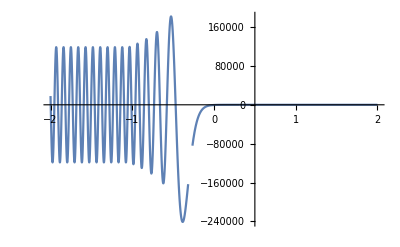

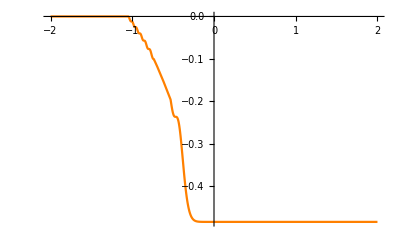

```mathematica
(*TM-wave*)
step=0.0000001;
Singularity =DSolveValue[D[y[x,x0],{x,2}]+(2a*x0/(2a*x0+ⅈ*Im[Epsilon[x0]]))*D[y[x,x0],x]-k^2*Sin[t]^2*y[x,x0]==0,y,{x,x0}];
x1=Sqrt[-Re[b]/a];
x2=-x1;

(*Right and simpliest part*)
TMRight = 
{Ereal'[x]==k*(Bimg[x]-Sin[t]^2*Im[(Breal[x]+ⅈ*Bimg[x])/Epsilon[x]]),
Eimg'[x]==k*(Sin[t]^2*Re[(Breal[x]+ⅈ*Bimg[x])/Epsilon[x]]-Breal[x]),
Breal'[x]==k*(Re[Epsilon[x]]*Eimg[x]+Im[Epsilon[x]]*Ereal[x]),
Bimg'[x]==-k*(Re[Epsilon[x]]*Ereal[x]-Im[Epsilon[x]]*Eimg[x]),
Ereal[X0]==A*Cos[t],Breal[X0]==-A,Eimg[X0]==Bimg[X0]==0};
{Ezr,Ezi,Byr,Byi}= NDSolveValue[TMRight,{Ereal,Eimg,Breal,Bimg},{x,x1+step,X0}];
EzReal=Plot[Ezr[x],{x,x1+step,X0}];

firstPoint=
{Singularity[x1+step,x1]==Ezr[x1+step]+ⅈ*Ezi[x1+step],
(D[Singularity[x,y],x]/.{x->x1+step,y->x1})==Ezr'[x1+step]+ⅈ*Ezi'[x1+step]};
firstSol=NSolve[firstPoint,{C[1][x1],C[2][x1]}];

(*Middle part*)
TMInner = 
{Ereal2'[x]==k*(Bimg2[x]-Sin[t]^2*Im[(Breal2[x]+ⅈ*Bimg2[x])/Epsilon[x]]),
Eimg2'[x]==k*(Sin[t]^2*Re[(Breal2[x]+ⅈ*Bimg2[x])/Epsilon[x]]-Breal2[x]),
Breal2'[x]==k*(Re[Epsilon[x]]*Eimg2[x]+Im[Epsilon[x]]*Ereal2[x]),
Bimg2'[x]==-k*(Re[Epsilon[x]]*Ereal2[x]-Im[Epsilon[x]]*Eimg2[x]),
Ereal2[x1-step]==(Re[Singularity[x1-step,x1]]/.firstSol),
Eimg2[x1-step]==(Im[Singularity[x1-step,x1]]/.firstSol),
Breal2[x1-step]==Re[ⅈ*Piecewise[{{1/k,t==0}},Epsilon[x1-step]/(Sin[t]*k^2*(Epsilon[x1-step]-Sin[t]^2))]*(D[Singularity[x,y],x]/.{x->x1-step,y->x1}/.firstSol)],
Bimg2[x1-step]==Im[ⅈ*Piecewise[{{1/k,t==0}},Epsilon[x1-step]/(Sin[t]*k^2*(Epsilon[x1-step]-Sin[t]^2))]*(D[Singularity[x,y],x]/.{x->x1-step,y->x1}/.firstSol)],
WhenEvent[Abs[x-x2]<step,{"StopIntegration" ,x2+step=x}]};
{Ezr2,Ezi2,Byr2,Byi2}= NDSolveValue[TMInner,{Ereal2,Eimg2,Breal2,Bimg2},{x,x2+step,x1-step}];
EzReal2=Plot[Ezr2[x],{x,x2+step,x1-step}];

secondPoint=
{Singularity[x2+step,x2]==Ezr2[x2+step]+ⅈ*Ezi2[x2+step],
(D[Singularity[x,y],x]/.{x->x2+step,y->x2})==Ezr2'[x2+step]+ⅈ*Ezi2'[x2+step]};
secondSol=NSolve[secondPoint,{C[1][x2],C[2][x2]}];

(*Last and most important part*)
TMLeft = 
{Ereal3'[x]==k*(Bimg3[x]-Sin[t]^2*Im[(Breal3[x]+ⅈ*Bimg3[x])/Epsilon[x]]),
Eimg3'[x]==k*(Sin[t]^2*Re[(Breal3[x]+ⅈ*Bimg3[x])/Epsilon[x]]-Breal3[x]),
Breal3'[x]==k*(Re[Epsilon[x]]*Eimg3[x]+Im[Epsilon[x]]*Ereal3[x]),
Bimg3'[x]==-k*(Re[Epsilon[x]]*Ereal3[x]-Im[Epsilon[x]]*Eimg3[x]),
Ereal3[x2-step]==(Re[Singularity[x2-step,x2]]/.secondSol),
Eimg3[x2-step]==(Im[Singularity[x2-step,x2]]/.secondSol),
Breal3[x2-step]==Re[ⅈ*Piecewise[{{1/k,t==0}},Epsilon[x2-step]/(Sin[t]*k^2*(Epsilon[x2-step]-Sin[t]^2))]*(D[Singularity[x,y],x]/.{x->x2-step,y->x2}/.secondSol)],
Bimg3[x2-step]==Im[ⅈ*Piecewise[{{1/k,t==0}},Epsilon[x2-step]/(Sin[t]*k^2*(Epsilon[x2-step]-Sin[t]^2))]*(D[Singularity[x,y],x]/.{x->x2-step,y->x2}/.secondSol)]};
{Ezr3,Ezi3,Byr3,Byi3}= NDSolveValue[TMLeft,{Ereal3,Eimg3,Breal3,Bimg3},{x,-X0,x2-step}];
EzReal3=Plot[Ezr3[x],{x,-X0,x2-step}];

Show[EzReal,EzReal2,EzReal3,PlotRange->Automatic]

S =Function[x,Piecewise[{
{Abs[Re[(Ezr[x]+ⅈ*Ezi[x])*(Byr[x]-ⅈ*Byi[x])]]*(1+Tan[t]^2)^0.5,x>x1+step},
{Abs[Re[(Ezr2[x]+ⅈ*Ezi2[x])*(Byr2[x]-ⅈ*Byi2[x])]]*(1+Tan[t]^2)^0.5,x1-step>x>x2+step},
{Abs[Re[(Ezr3[x]+ⅈ*Ezi3[x])*(Byr3[x]-ⅈ*Byi3[x])]]*(1+Tan[t]^2)^0.5,x2-step>x}}]];
power=Plot[S[x],{x,-X0,X0},PlotStyle->{Bold,Orange}];

Lost=Function[x,(S[x]-S[-X0])/S[-X0]];
Plot[Lost[x],{x,-X0,X0},PlotStyle->{Bold,Orange}]
```

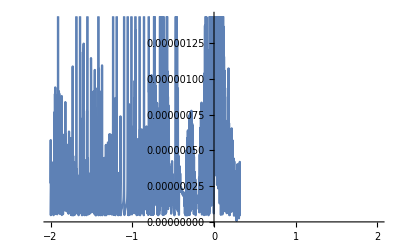

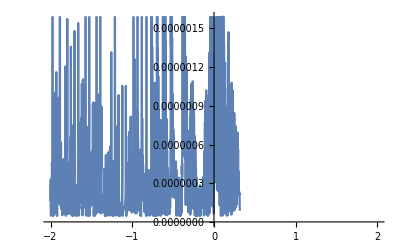

```mathematica
ETM=Function[x,Piecewise[{{Ezr3[x]+ⅈ*Ezi3[x],x<x2},{Ezr2[x]+ⅈ*Ezi2[x],x2<x<x1},{Ezr[x]+ⅈ*Ezi[x],x>x1}}]];
ETE = Function[x,Eyr[x]+ⅈ*Eyi[x]];
Plot[Abs[ETE[x]-ETM[x]]/Min[Abs[ETE[x]],Abs[ETM[x]]],{x,-X0,X0}]

BTM=Function[x,Piecewise[{{Byr3[x]+ⅈ*Byi3[x],x<x2},{Byr2[x]+ⅈ*Byi2[x],x2<x<x1},{Byr[x]+ⅈ*Byi[x],x>x1}}]];
BTE = Function[x,Bzr[x]+ⅈ*Bzi[x]];
Plot[Abs[BTE[x]+BTM[x]]/Min[Abs[BTE[x]],Abs[BTM[x]]],{x,-X0,X0}]
```